Приложение Г.

```mathematica
Needs["Splines`"];
```

```mathematica
(*Введеём начальные значения, по которым будем строить сплайн*)
```

```mathematica
n=3;
```

```mathematica
Uzl={0.1,0.3,0.7,1.4};
```

```mathematica
Znach={1,-7,15,25};
```

```mathematica
dF={-7,10,22,7};
```

```mathematica
Do[{Subscript[x, i]=Uzl⟦i+1⟧,Subscript[f, i]=Znach⟦i+1⟧,Subscript[df, i]=dF⟦i+1⟧},{i,0,n}]
```

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]},
PlotRange->{{0,1.5},{-40,40}}];
```

```mathematica
(*Рассмотрим построение сплайна Шенберга - Subscript[S, 3,1](x)*)
```

```mathematica
Subscript[P, k_][X_]:=Subscript[f, k]+(X-Subscript[x, k])*(Subscript[A, k]*X^2+Subscript[B, k] X+Subscript[C, k]);
```

```mathematica
eq1=Table[Subscript[P, k][Subscript[x, k+1]]==Subscript[P, k+1][Subscript[x, k+1]],{k,0,n-2}];
```

```mathematica
eq2={Subscript[P, n-1][Subscript[x, n]]==Subscript[f, n]};
```

```mathematica
eq3=Table[Subscript[P, k]'[Subscript[x, k+1]]==Subscript[P, k+1]'[Subscript[x, k+1]],{k,0,n-2}];
```

```mathematica
eq4={Subscript[P, 0]''[Subscript[x, 0]]==0};
```

```mathematica
eq5=Table[Subscript[P, k]''[Subscript[x, k+1]]==Subscript[P, k+1]''[Subscript[x, k+1]],{k,0,n-2}];
```

```mathematica
eq6={Subscript[P, n-1]''[Subscript[x, n]]==0};
```

```mathematica
eq=Join[eq1,eq2,eq3,eq4,eq5,eq6]
```

{1+0.2 (0.09 A_0+0.3 B_0+C_0)==-7.,-7+0.4 (0.49 A_1+0.7 B_1+C_1)==15.,15+0.7 (1.96 A_2+1.4 B_2+C_2)==25,0.09 A_0+0.3 B_0+0.2 (0.6 A_0+B_0)+C_0==0.+0.09 A_1+0.3 B_1+C_1,0.49 A_1+0.7 B_1+0.4 (1.4 A_1+B_1)+C_1==0.+0.49 A_2+0.7 B_2+C_2,0.+0.4 A_0+2 B_0==0,1.6 A_0+2 B_0==0.+1.2 A_1+2 B_1,3.6 A_1+2 B_1==0.+2.8 A_2+2 B_2,7. A_2+2 B_2==0}

```mathematica
koef=Solve[eq,{}]//Flatten
```

{A_0→454.205,A_1→-314.66,A_2→50.0329,B_0→-90.841,B_1→461.319,B_2→-175.115,C_0→-53.6262,C_1→-113.74,C_2→161.382}

```mathematica
Spl[X_]=Table [Subscript[P, k][X]/.koef,{k,0,n-1}]//Expand
```

{6.36262-44.5421 X-136.262 X^2+454.205 X^3,27.122-252.136 X+555.717 X^2-314.66 X^3,-97.9677+283.963 X-210.138 X^2+50.0329 X^3}

```mathematica
Gr4=Table[Plot[Spl[X][[k]],{X,Subscript[x, k-1],Subscript[x, k]}],{k,1,n}];
```

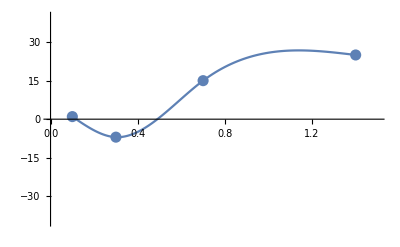

```mathematica
Show[Gr1,Gr4]
```

```mathematica
(*Проверим построенный сплайн встроенной функцией Spline(показана красной штриховкой)*)
```

```mathematica
Points={{0.1,1},{0.3,-7},{0.7,15},{1.4,25}};
```

```mathematica
GrH1=Graphics[{Red,Dashed,Spline[Points,Cubic]}];
```

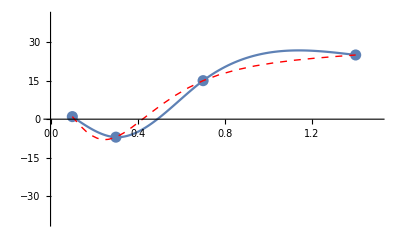

```mathematica
Show[Gr1,Gr4,GrH1]
```